## Cubic Root solver For Ellipse calculations

## Cubic Solver

```mathematica
p[a_,b_,c_]:=(3 a c - b^2)/(3 a^2)
q[a_,b_,c_,d_]:=(2 b^3-9 a b c +27 a^2 d)/(27 a^3)
t[k_,a_,b_,c_,d_]:=2 √(-p[a,b,c]/3)Cos[1/3 ArcCos[(3 q[a,b,c,d])/(2p[a,b,c])√(-3/p[a,b,c])]-(2 π k)/3]
pqCheck[a_,b_,c_,d_]:=4 p[a,b,c]^3+27 q[a,b,c,d]^2

cuberoot[k_,a_,b_,c_,d_]:=t[k,a,b,c,d]-b/(3 a)
```

## a in terms of x and ℓ

### Cubic form

ℓ=a-a^3/x^2
a^3/x^2-a+ℓ==0
a^3-a x^2+ℓx^2==0
a^3+0 a^2-x^2 a +ℓx^2==0

### Find roots

```mathematica
acoeff=1; bcoeff=0; ccoeff=- x^2;dcoeff =x^2 ℓ;
```

need to see if a equals 1.5

#### 0 Root

```mathematica
r0=FullSimplify[cuberoot[0,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
FullSimplify[√r0,x>0 && ℓ > 0]
r0/.x->2.0125 /.ℓ-> 2/3 //N
```

(2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)

(√2 √(x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]]))/3^(1/4)

1.50005

#### 1 Root

```mathematica
r1=FullSimplify[cuberoot[1,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r1/.x->2.0125 /.ℓ-> 2/3 //N
```

(2 x Sin[1/3 ArcSin[(3 √3 ℓ)/(2 x)]])/(√3)

0.787034

#### 2 Root

```mathematica
r2=FullSimplify[cuberoot[2,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r2/.x->2.0125 /.ℓ-> 2/3 //N
```

-(2 x Cos[1/3 ArcCos[(3 √3 ℓ)/(2 x)]])/(√3)

-2.28708

### Answer

```mathematica
a=(2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)//FullSimplify
```

(2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)

```mathematica
Plot3D[(2 a^2/(√(a^2-b^2)) Cos[1/3 ArcCos[-(3 √3 b^2/a)/(2 a^2/(√(a^2-b^2)))]])/(√3)-a,{a,0,6},{b,0,a}]
Plot3D[(2 a^2/(√(a^2-b^2))Sin[1/3 ArcSin[(3 √3 b^2/a)/(2 a^2/(√(a^2-b^2)))]])/(√3)-a,{a,0,6},{b,0,a}]
```

-Graphics3D-

-Graphics3D-

## b in terms of x and ℓ

```mathematica
b=√(c p)
```

```mathematica
FullSimplify[√(2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])*1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])),x>0 && ℓ > 0]
```

1/3 √2 x √(Cos[2/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]-Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

```mathematica
1/3 √2 x √(Cos[2/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]-Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])
```

```mathematica
u=1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]
```

```mathematica
1/3 √2 x √(Cos[2 u ]-Sin[u])//FullSimplify
```

```mathematica
1/3 √2 x √(1-2 Sin[u]^2-Sin[u])
```

1/3 √2 x √(1-Sin[u]-2 Sin[u]^2)

```mathematica
1-2 Sin[u]^2-Sin[u]//FullSimplify
```

Cos[2 u]-Sin[u]

```mathematica
FullSimplify[√(2/3 x (1+Sin[u])*1/3 (x-2 x Sin[u])),x>0 && u> 0]
```

1/3 √2 x √(Cos[2 u]-Sin[u])

```mathematica
1/3 √2 x √(Cos[2/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]-Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])/.x->2.0125 /.ℓ-> 2/3 //N
```

1.00002

### Plot Check

```mathematica
Plot3D[1/3 √2 a^2/(√(a^2-b^2))√(Cos[2/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]]-Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]])-b,{a,0,6},{b,0,a}]
```

-Graphics3D-

### Cubic form

ℓ=(b √(1+(√(-4 b^2 x^2+x^4))/x^2))/(√2)
ℓ=√(b^2/2+b^2/(2 x^2)√(-4 b^2 x^2+x^4))
ℓ^2=b^2/2+b^2/(2 x^2)√(-4 b^2 x^2+x^4)
ℓ^2=b^2/2+b^2/(2x)√(-4 b^2 +x^2)
(ℓ^2-b^2/2)/(b^2/(2x))=√(-4 b^2 +x^2)
(ℓ^2-b^2/2)/(b^2/(2x))=√(-4 b^2 +x^2)

```mathematica
Expand[Simplify[((ℓ^2-b^2/2)/(b^2/(2x)))^2,x>0 && b> 0]]
```

x^2-(4 x^2 ℓ^2)/b^2+(4 x^2 ℓ^4)/b^4

x^2-(4 x^2 ℓ^2)/b^2+(4 x^2 ℓ^4)/b^4=-4 b^2 +x^2
b^4 x^2-(b^4 4 x^2 ℓ^2)/b^2+(b^4 4 x^2 ℓ^4)/b^4=-4 b^4 b^2 +b^4 x^2
b^4 x^2-b^2 4 x^2 ℓ^2+4 x^2 ℓ^4=-4 b^6+b^4 x^2
4 b^6+2 b^4 x^2-b^2 4 x^2 ℓ^2+4 x^2 ℓ^4=0

```mathematica
√(4 b^6+2 b^4 x^2-b^2 4 x^2 ℓ^2+4 x^2 ℓ^4)//FullSimplify
```

√(4 b^6+2 b^4 x^2-4 b^2 x^2 ℓ^2+4 x^2 ℓ^4)

x→b^3/(ℓ √(b^2-ℓ^2))
x ℓ √(b^2-ℓ^2)= b^3
 √(b^2 x^2 ℓ^2-x^2 ℓ^4)= √(b^6)
 b^2 x^2 ℓ^2-x^2 ℓ^4= b^6
 b^6- b^2 x^2 ℓ^2+x^2 ℓ^4 = 0

```mathematica
b^6- b^2 x^2 ℓ^2+x^2 ℓ^4//FullSimplify
```

b^6-b^2 x^2 ℓ^2+x^2 ℓ^4

```mathematica
r sub r=b^2
```

```mathematica
r^3-r x^2 ℓ^2+x^2 ℓ^4
```

### Find roots

```mathematica
acoeff=1; bcoeff=-x^2 ℓ^2; ccoeff=0 ;dcoeff =x^2 ℓ^4;
```

need to see if b equals ???

#### 0 Root

```mathematica
r0=FullSimplify[cuberoot[0,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
FullSimplify[√r0,x>0 && ℓ > 0]
r0/.x->2.0125 /.ℓ-> 2/3 //N
```

1/3 (x^2 ℓ^2+2 √3 Cos[1/3 ArcCos[(x^2 ℓ^4 (-27+2 x^4 ℓ^2) (-1/((1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))[1,-x^2 ℓ^2,0]))^(3/2))/(6 √3)]] √(-(1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))[1,-x^2 ℓ^2,0]))

1/(√3)(√(x^2 ℓ^2+2 √3 Cos[1/3 ArcCos[(x^2 ℓ^4 (-27+2 x^4 ℓ^2) (-1/((1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))[1,-x^2 ℓ^2,0]))^(3/2))/(6 √3)]] √(-(1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))[1,-x^2 ℓ^2,0])))

0.333333 (1.80007+3.4641 √(-1. 0.894416[1.,-1.80007,0.]) Cos[0.333333 ArcCos[-0.956042 (-1./(0.894416[1.,-1.80007,0.]))^(3/2)]])

#### 1 Root

```mathematica
r1=FullSimplify[cuberoot[1,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r1/.x->2.0125 /.ℓ-> 2/3 //N
```

2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

1.11808

#### 2 Root

```mathematica
r2=FullSimplify[cuberoot[2,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r2/.x->2.0125 /.ℓ-> 2/3 //N
```

4/3 x Sin[1/6 ArcCos[1-(27 ℓ^2)/(2 x^2)]]^2

0.307788

### Answer

```mathematica
c=2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])//FullSimplify
```

2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

## c in terms of x and ℓ

### Cubic form

ℓ=(√c (c-x))/(√x)
√x ℓ=√c (c-x)
√x ℓ=√(c^3)-√c x
√x ℓ=√(c^3)-√c x
x ℓ^2=c^3-2 c^2 x+c x^2
c^3-2 c^2 x+c x^2-x ℓ^2 = 0

### Find roots

```mathematica
acoeff=1; bcoeff=-2x; ccoeff=x^2 ;dcoeff =-x ℓ^2;
```

need to see if c equals 1.1180

#### 0 Root

```mathematica
r0=FullSimplify[cuberoot[0,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r0/.x->2.0125 /.ℓ-> 2/3 //N
```

4/3 x Cos[1/6 ArcCos[-1+(27 ℓ^2)/(2 x^2)]]^2

2.59913

#### 1 Root

```mathematica
r1=FullSimplify[cuberoot[1,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r1/.x->2.0125 /.ℓ-> 2/3 //N
```

2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

1.11808

#### 2 Root

```mathematica
r2=FullSimplify[cuberoot[2,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r2/.x->2.0125 /.ℓ-> 2/3 //N
```

4/3 x Sin[1/6 ArcCos[1-(27 ℓ^2)/(2 x^2)]]^2

0.307788

### Answer

```mathematica
c=2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])//FullSimplify
```

2/3 x (1+Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

### Plot Check

```mathematica
Plot3D[2/3 a^2/(√(a^2-b^2))(1+Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]])-√(a^2-b^2),{a,0,6},{b,0,a}]
```

-Graphics3D-

```mathematica
2/3 a^2/(√(a^2-b^2))(1+Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]])-√(a^2-b^2)/.a->6/.b->4.5//N
```

-4.44089×10^-16

```mathematica
2/3 a^2/(√(a^2-b^2))(1+Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]])/.a->6/.b->5.95//N
```

40.2239

## e in terms of x and ℓ

### Cubic form

x→ℓ/(e-e^3)
(e-e^3)x =ℓ
-e^3+0 e^2+e-ℓ/x=0
e^3+0 e^2-e+ℓ/x=0

### Find roots

```mathematica
acoeff=1; bcoeff=0; ccoeff=-1 ;dcoeff =ℓ/x;
```

```mathematica
(2/3)/0.8944156894431008//N
```

0.745366

need to see if e equals 0.745366

#### 0 Root

```mathematica
r0=FullSimplify[cuberoot[0,acoeff,bcoeff,ccoeff,dcoeff]]
r0/.x->2.0125 /.ℓ-> 2/3 //N
```

(2 Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)

0.745366

#### 1 Root

```mathematica
r1=FullSimplify[cuberoot[1,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r1/.x->2.0125 /.ℓ-> 2/3 //N
```

(2 Sin[1/3 ArcSin[(3 √3 ℓ)/(2 x)]])/(√3)

0.391073

#### 2 Root

```mathematica
r2=FullSimplify[cuberoot[2,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r2/.x->2.0125 /.ℓ-> 2/3 //N
```

-(2 Cos[1/3 ArcCos[(3 √3 ℓ)/(2 x)]])/(√3)

-1.13644

### Answer

```mathematica
e=(2 Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)//FullSimplify
```

(2 Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)

### Plot Check

```mathematica
Plot3D[(2 Sin[1/3 ArcSin[(3 √3 b^2/a)/(2 a^2/(√(a^2-b^2)))]])/(√3)-√(1-b^2/a^2),{a,0,6},{b,0,a},PlotRange->All]
```

-Graphics3D-

```mathematica
(2 Sin[1/3 ArcSin[(3 √3 b^2/a)/(2 a^2/(√(a^2-b^2)))]])/(√3)-√(1-b^2/a^2)/.a->6
```

-√(1-b^2/36)+(2 Sin[1/3 ArcSin[(b^2 √(36-b^2))/(48 √3)]])/(√3)

```mathematica
Solve[{-√(1-b^2/36)+(2 Sin[1/3 ArcSin[(b^2 √(36-b^2))/(48 √3)]])/(√3) == 0,b>0,b<6}, b]
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{{}}

```mathematica
(2 Cos[1/3 ArcCos[-(3 √3 b^2/a)/(2 a^2/(√(a^2-b^2)))]])/(√3)/.a->10000/.b->8500//N
```

0.626482

## p in terms of x and ℓ

### Cubic form

ℓ→p √(1-p/x)
ℓ=√(p^2-p^3/x)
ℓ^2=p^2-p^3/x
p^3/x-p^2-0p+ℓ^2 =0
a=1/x b=-1 c=0 d =ℓ^2

### Find roots

```mathematica
acoeff=1/x; bcoeff=-1; ccoeff=0 ;dcoeff =ℓ^2;
```

need to see if p equals 0.89441

#### 0 Root

```mathematica
r0=FullSimplify[cuberoot[0,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r0/.x->2.0125 /.ℓ-> 2/3 //N
```

1/3 x (1+2 Cos[1/3 ArcCos[1-(27 ℓ^2)/(2 x^2)]])

1.70471

#### 1 Root

```mathematica
r1=FullSimplify[cuberoot[1,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r1/.x->2.0125 /.ℓ-> 2/3 //N
```

1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

0.894416

#### 2 Root

```mathematica
r2=FullSimplify[cuberoot[2,acoeff,bcoeff,ccoeff,dcoeff],x>0 && ℓ > 0]
r2/.x->2.0125 /.ℓ-> 2/3 //N
```

1/3 (x-2 x Sin[1/6 (π+2 ArcCos[1-(27 ℓ^2)/(2 x^2)])])

-0.586628

### Answer

```mathematica
p=1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])
```

1/3 (x-2 x Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]])

### Plot Check

```mathematica
Plot3D[1/3 (a^2/(√(a^2-b^2))-2 a^2/(√(a^2-b^2)) Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]])-b^2/(√(a^2-b^2)),{a,0,6},{b,0,a}]
```

-Graphics3D-

```mathematica
Sin[1/3 ArcSin[1-(27 (b^2/a)^2)/(2 (a^2/(√(a^2-b^2)))^2)]]/.a->5
```

Sin[1/3 ArcSin[1-(27 b^4 (25-b^2))/31250]]

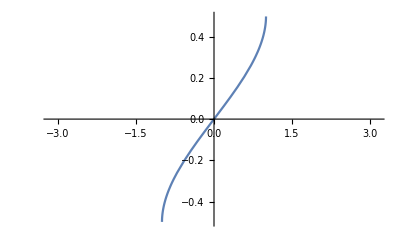

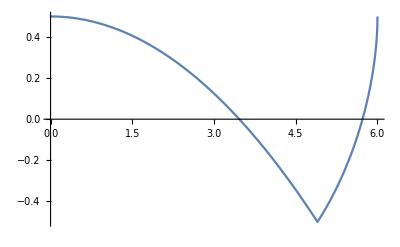

```mathematica
Plot[Sin[1/3 ArcSin[x]],{x,-π,π}]
Plot[Sin[1/3 ArcSin[1-(b^4 (36-b^2))/3456]],{b,0,6}]
```

```mathematica
FindMinimum[Sin[1/3 ArcSin[1-(b^4 (36-b^2))/3456]],{b,1,5.8}]
```

{-0.5,{b→4.89898}}

```mathematica
4.898979489103387/6
```

0.816497

```mathematica
FindMinimum[Sin[1/3 ArcSin[1-(27 b^4 (25-b^2))/31250]],{b,1,4.9}]
```

{-0.5,{b→4.08248}}

```mathematica
4.082482905276168/5
```

0.816497

```mathematica
b/a>√(2/3)//N
```

```mathematica
1-(4.898979489103387^4 (36-4.898979489103387^2))/3456
```

-1.

```mathematica
RootApproximant[0.8164965810552337]
```

√(2/3)

```mathematica
(1/3 √2 x √(Cos[2/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]-Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))/((2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3))//FullSimplify
```

(Sec[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]] √(Cos[2/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]-Sin[1/3 ArcSin[1-(27 ℓ^2)/(2 x^2)]]))/(√6)

```mathematica
(2 Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)
```

## Find inflextion

### Try 1

```mathematica
(2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)/.x->2.0125
```

2.32383 Cos[1/3 ArcCos[-1.29097 ℓ]]

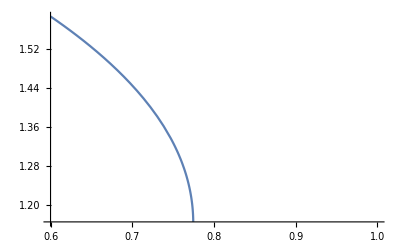

```mathematica
Plot[2.3238348334882444 Cos[1/3 ArcCos[-1.2909695460140698 ℓ]],{ℓ,.6,1}]
```

```mathematica
FindMinimum[2.3238348334882444 Cos[1/3 ArcCos[-1.2909695460140698 ℓ]],{ℓ,.6,.7}]
```

FindMinimum[2.32383 Cos[1/3 ArcCos[-1.29097 ℓ]],{ℓ,0.6,0.7}]

```mathematica
FindMinimum[Re[2.3238348334882444 Cos[1/3 ArcCos[-1.2909695460140698 ℓ]]],{ℓ,0.6,.1}]
```

{1.16192,{ℓ→0.774612}}

```mathematica
RootApproximant[0.7746116204616134/2.0125]
```

5302/13775

```mathematica
ToRadicals[RootApproximant[2.0125/0.7746116204616134,4]]
```

13775/5302

```mathematica
2.3238348334882444 Cos[1/3 ArcCos[-1.2909695460140698 ℓ]]/.ℓ->2
```

1.33153+1.12639 ⅈ

### Try 2

```mathematica
(2 x Cos[1/3 ArcCos[-(3 √3 ℓ)/(2 x)]])/(√3)/.x->3
```

2 √3 Cos[1/3 ArcCos[-(√3 ℓ)/2]]

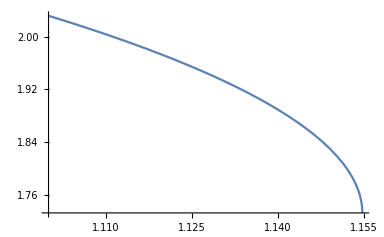

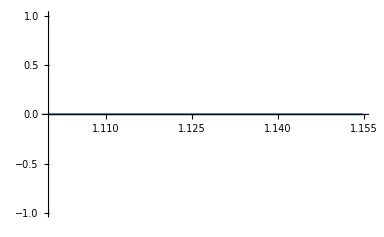

```mathematica
Plot[Re[2 √3 Cos[1/3 ArcCos[-(√3 ℓ)/2]]],{ℓ,1.1,1.154700}]
Plot[Im[2 √3 Cos[1/3 ArcCos[-(√3 ℓ)/2]]],{ℓ,1.1,1.154700}]
```